## 对单一变量的拟合

在以下计算过程中，我们只考虑单一因素对产量的影响。

```mathematica
data1992={0,28,56,84,112,168,224,280,336,392,11.02,12.70,14.56,6.17,17.25,22.59,21.63,19.34,16.12,14.11,0,49,98,147,196,294,394,489,587,685,6.39,9.48,12.46,14.33,17.10,21.94,22.64,21.34,22.07,24.53,0,47,93,140,168,279,372,465,554,651,15.75,16.76,16.89,16.24,17.56,19.20,17.97,15.84,20.11,19.40};
len=Length[data1992]/6;
```

```mathematica
data1992N=Table[data1992[[{i,i+len}]],{i,1,10}]
data1992P=Table[data1992[[{i+2len,i+3len}]],{i,1,10}]
data1992K=Table[data1992[[{i+4len,i+5len}]],{i,1,10}]
```

{{0,11.02},{28,12.7},{56,14.56},{84,6.17},{112,17.25},{168,22.59},{224,21.63},{280,19.34},{336,16.12},{392,14.11}}

{{0,6.39},{49,9.48},{98,12.46},{147,14.33},{196,17.1},{294,21.94},{394,22.64},{489,21.34},{587,22.07},{685,24.53}}

{{0,15.75},{47,16.76},{93,16.89},{140,16.24},{168,17.56},{279,19.2},{372,17.97},{465,15.84},{554,20.11},{651,19.4}}

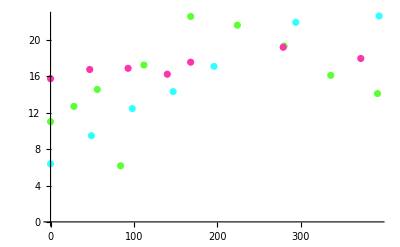

```mathematica
pointN=ListPlot[data1992N,PlotStyle->Hue[0.3,0.8,1]];
pointP=ListPlot[data1992P,PlotStyle->Hue[0.5,0.8,1]];
pointK=ListPlot[data1992K,PlotStyle->Hue[0.9,0.8,1]];
Show[pointN,pointK,pointP]
```

```mathematica
(*删除不合理数据*)
data1992Nfix={{0,11.02},{28,12.7},{56,14.56},{112,17.25},{168,22.59},{224,21.63},{280,19.34},{336,16.12},{392,14.11}}
```

{{0,11.02},{28,12.7},{56,14.56},{112,17.25},{168,22.59},{224,21.63},{280,19.34},{336,16.12},{392,14.11}}

```mathematica
(*选择合适的函数方程进行拟合N元素*)
modelForNbase=Piecewise[{{a*x+b,x<d},{c*x+(a-c)*d+b,x≥d}}];
control={d≥180,d<220};
approxNbase=FindFit[data1992Nfix,{modelForNbase,control},{a,b,c,d},x];
paramsNbase=modelForNbase/.approxNbase;
modelForN=paramsNbase*(a*Sin[d*x+c]+b);
control={d<0.105,d>0};
approxN=FindFit[data1992Nfix,{modelForN,control},{a,b,c,d},x];
paramsN=modelForN/.approxN;

approxNfunc=Plot[paramsN,{x,0,400},PlotStyle->Red];
```

```mathematica
(*选择合适的函数方程进行拟合P元素*)
approxP=Fit[data1992P,{1,x,x^2,x^3,x^5,x^7},x]
approxPfunc=Plot[approxP,{x,0,700},PlotStyle->Blue];
```

6.67991+0.0408814 x+0.000190559 x^2-6.16632×10^-7 x^3+9.02753×10^-13 x^5-5.29584×10^-19 x^7

```mathematica
(*选择合适的函数方程进行拟合K元素*)
modelForKbase=d*x^3+e*x^4+f*x^5+a*x^2+b*x+c+g*x^6+h*x^7+i*h*x^8;
approxKbase=FindFit[data1992K,modelForKbase,{a,b,c,d,e,f,g,h,i},x];
paramsKbase=modelForKbase/.approxKbase;
modelForK=paramsKbase*(a*Sin[d*x+c]+b);
control={d<0.105,d>0};
approxK=FindFit[data1992K,{modelForK,control},{a,b,c,d},x];
paramsK=modelForK/.approxK
approxKfunc=Plot[paramsK,{x,0,700},PlotStyle->Green];
```

(15.7412+0.0573014 x-0.00101475 x^2+7.02167×10^-6 x^3-1.88113×10^-8 x^4+1.47454×10^-11 x^5+7.70014×10^-15 x^6-1.4508×10^-20 x^7-1.46214×10^-20 x^8) (1.00107+0.00958012 Sin[129.517+0.0517615 x])

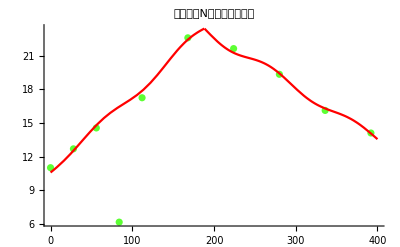

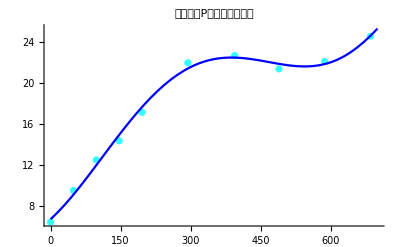

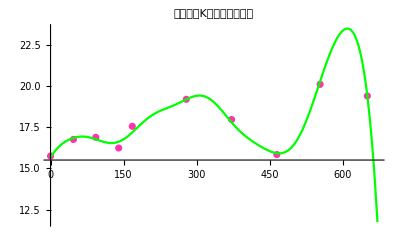

```mathematica
(*绘图*)
Show[{pointN,approxNfunc},PlotRange->All,PlotLabel->"生菜的施N量与产量的拟合"]
Show[{pointP,approxPfunc},PlotRange->All,PlotLabel->"生菜的施P量与产量的拟合"]
Show[{pointK,approxKfunc},PlotRange->All,PlotLabel->"生菜的施K量与产量的拟合"]
```

```mathematica
(*计算N的相关系数(删除不合理数据)*)
factN=Transpose[data1992Nfix][[2]];
predictionN=Table[paramsN/.{x->data1992Nfix[[i,1]]},{i,1,len-1}];
Correlation[factN,predictionN]
```

0.996679

```mathematica
(*计算P的相关系数*)
factP=Transpose[data1992P][[2]];
predictionP=Table[approxP/.{x->data1992P[[i,1]]},{i,1,len}];
Correlation[factP,predictionP]
```

0.997463

```mathematica
(*计算K的相关系数*)
factP=Transpose[data1992K][[2]];
predictionP=Table[paramsK/.{x->data1992K[[i,1]]},{i,1,len}];
Correlation[factP,predictionP]
```

0.991171

## 对多变量共同作用的拟合

在此时，我们同时考虑多种因素的复合影响，这一过程更有实际意义。

```mathematica
data1992Mix={};
Do[data1992Mix=Append[data1992Mix,{data1992Nfix[[i,1]],data1992P[[7,1]],data1992K[[7,1]],data1992Nfix[[i,2]]}],{i,1,len-1}];
Do[data1992Mix=Append[data1992Mix,{data1992N[[7,1]],data1992P[[i,1]],data1992K[[7,1]],data1992P[[i,2]]}],{i,1,len}];
Do[data1992Mix=Append[data1992Mix,{data1992N[[7,1]],data1992P[[7,1]],data1992K[[i,1]],data1992K[[i,2]]}],{i,1,len}];
data1992Mix
```

{{0,394,372,11.02},{28,394,372,12.7},{56,394,372,14.56},{112,394,372,17.25},{168,394,372,22.59},{224,394,372,21.63},{280,394,372,19.34},{336,394,372,16.12},{392,394,372,14.11},{224,0,372,6.39},{224,49,372,9.48},{224,98,372,12.46},{224,147,372,14.33},{224,196,372,17.1},{224,294,372,21.94},{224,394,372,22.64},{224,489,372,21.34},{224,587,372,22.07},{224,685,372,24.53},{224,394,0,15.75},{224,394,47,16.76},{224,394,93,16.89},{224,394,140,16.24},{224,394,168,17.56},{224,394,279,19.2},{224,394,372,17.97},{224,394,465,15.84},{224,394,554,20.11},{224,394,651,19.4}}

```mathematica
modelAll=a*x+b*y+c*z+d*x*y+e*x*z+f*y*z+g*x*x+h*y*y+i*z*z+j*x*y*z+z*k*Sin[l*x*y*z+m]+n*Abs[o*x*y*z-p];
result=FindFit[data1992Mix,{modelAll},{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r},{x,y,z}];
ParamsAll=modelAll/.result
```

115896. x-0.00020587 x^2-5382.36 y-270.114 x y-0.0000192176 y^2-23721.9 z-205.636 x z+74.6822 y z+0.758972 x y z-0.0000347199 z^2-1.90373 Abs[-424.956-0.158463 x y z]-0.00410014 z Sin[2.11557+1. x y z]

```mathematica
factAll=Join[Transpose[data1992Nfix][[2]],Transpose[data1992P][[2]],Transpose[data1992K][[2]]];
predictall=Table[ParamsAll/.{x->data1992Mix[[i,1]],y->data1992Mix[[i,2]],z->data1992Mix[[i,3]]},{i,1,3*len-1}];
Correlation[factAll,predictall]
```

0.946953